#### Fresnel Equation Setup

```mathematica
θt[θ_]:=ArcSin[Sin[θ]/n];
t1[θ_]:=(2 Cos[θ])/(Cos[θt[θ]]+n Cos[θ]);

r[θ_]:=(n Cos[θ]-Cos[θt[θ]])/(n Cos[θ]+Cos[θt[θ]]);
ψ[θ_]:=θ-θt[θ];
c=3*10^8;
```

#### Momentum after first Interaction

```mathematica
Clear[Pinitial,Preflection,Ptransmission,Pfinal1]
Pinitial=P{-1,0,0};
Preflection[θ_]=P(r[θ])^2{Cos[2θ],Sin[2θ],0};
Ptransmission[θ_]=-P(((t1[θ])^2 n Cos[θt[θ]])/Cos[θ]){Cos[ψ[θ]],Sin[ψ[θ]],0};
Pfinal1[θ_]=Preflection[θ]+Ptransmission[θ];
```

After Second Interaction

```mathematica
t2[θ_]:=(2 n Cos[ψ[θ]])/(n Cos[ψ[θ]-θt2]+ Cos[ψ[θ]]);
r2[θ_]:=(Cos[ψ[θ]]-n Cos[ψ[θ]-θt2])/(Cos[ψ[θ]]+n Cos[ψ[θ]-θt2]);
θt2=ArcSin[Sin[ψ[θ]]/1];
```

```mathematica
Preflection2=If[ψ<ArcSin[1/n],
P(((t1[θ])^2 n Cos[θt])/Cos[θ])(r2[θ])^2{Cos[ψ],-Sin[ψ]},
0];
```

```mathematica
Ptransmission2=P(((t1[θ])^2 n Cos[θt])/Cos[θ])(((t2[θ])^2 Cos[)/□
```

```mathematica
Pfinal2=
```

And the final optical momentum...

```mathematica
Pfinal=P r {Cos[2 θ],Sin[2 θ],0}+Pfinal2;
```

```mathematica
Pfinal
```

{P r Cos[2 θ]+1/300000000 n P t1 (r2 Cos[2 (θ-ArcSin[Sin[θ]/n])]-t2 Cos[θ-ArcSin[Sin[θ]/n]-ArcSin[Sin[θ-ArcSin[Sin[θ]/n]]]]),P r Sin[2 θ]+1/300000000 n P t1 (r2 Sin[2 (θ-ArcSin[Sin[θ]/n])]-t2 Sin[θ-ArcSin[Sin[θ]/n]-ArcSin[Sin[θ-ArcSin[Sin[θ]/n]]]]),0}

```mathematica
Clear[ΔP,CoM,rr]
ΔP[θ_]=Pinitial-Pfinal1[θ];
CoM[ϕ_]=(4 R)/(3 π){Cos[ϕ],Sin[ϕ],0};
rr[θ_,ϕ_]=R{Cos[θ],Sin[θ],0}-CoM[ϕ];
```

#### Torque about CoM

```mathematica
Clear[dτ]
dτ[θ_,ϕ_]=Cross[rr[θ,ϕ],ΔP[θ]];
Simplify[dτ[θ,0]]
dτ[1,0]/.n->1.5/.R->1/.P->1
```

{0,0,(P R (2 n^2 Cos[θ] (-8-6 (1+2 n^2) π Cos[θ]-3 √2 n π √((-1+2 n^2+Cos[2 θ])/n^2)+3 √2 n^2 π √((-1+2 n^2+Cos[2 θ])/n^2)+3 √2 n π √((-1+2 n^2+Cos[2 θ])/n^2) Cos[θ-ArcSin[Sin[θ]/n]]+6 n^2 π Cos[2 θ-ArcSin[Sin[θ]/n]]) Sin[θ]^3+8 Cos[θ] Sin[θ]^5+(4 n^4+6 n^5 π √(1-Sin[θ]^2/n^2)) Sin[2 θ]+n^5 Cos[θ] (-4+3 π Cos[θ]) (8 n Cos[θ]+√2 √((-1+2 n^2+Cos[2 θ])/n^2) (2+n^2+n^2 Cos[2 θ])) Sin[θ-ArcSin[Sin[θ]/n]]+1/2 n^3 (16 n-3 √2 π √((-1+2 n^2+Cos[2 θ])/n^2)) Sin[2 θ]^2 Sin[θ-ArcSin[Sin[θ]/n]]+n^4 Sin[2 θ]^3 (2-3 π Csc[θ] Sin[θ-ArcSin[Sin[θ]/n]])+Sin[θ] (3 n^4 π+8 n^8 Cos[θ]^5-6 n^8 π Cos[θ]^6+3 n^4 π Cos[2 θ]+3 n^6 π Cos[θ]^4 (4+n^2+n^2 Cos[2 θ])-6 n^4 π Cos[θ]^2 (1-3 n^2+n^2 Cos[2 θ]+4 n^2 Cos[θ-ArcSin[Sin[θ]/n]])-12 n^5 π Cos[θ] Cos[θ-ArcSin[Sin[θ]/n]] √(1-Sin[θ]^2/n^2)-4 n^6 Cos[θ]^3 (4-3 n π √(1-Sin[θ]^2/n^2)+3 n π Cos[θ-ArcSin[Sin[θ]/n]] √(1-Sin[θ]^2/n^2))+3 n^2 π Sin[2 θ]^2+8 n^3 √(1-Sin[θ]^2/n^2) Sin[2 θ] Sin[θ-ArcSin[Sin[θ]/n]])))/(3 π (n^2 Cos[θ]+n √(1-Sin[θ]^2/n^2))^4)}

{0,0,0.113517}

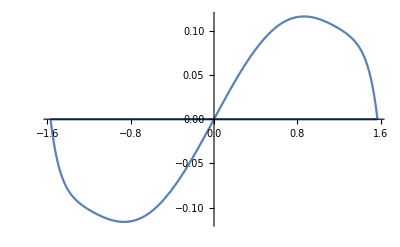

```mathematica
Plot[dτ[θ,0]/.n->1.5/.R->1/.P->1,{θ,-π/2,π/2}]
```

```mathematica
τ=Integrate[dτ[θ,0],{θ,-π/2,π/2}]
```

$Aborted

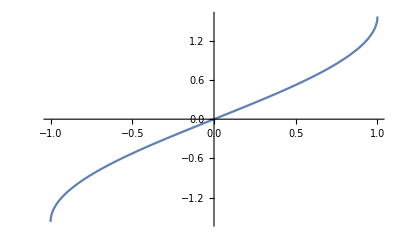

```mathematica
Plot[ArcSin[x],{x,-1,1}]
```

```mathematica
t1[0]
```

2/(n+√(1-Sin[θ]^2/n^2))

```mathematica
pf[θ_]:=P(r[θ]^2){Cos[2θ],Sin[2 θ],0}+P(((t1[θ])^2 n Cos[θt[θ]])/Cos[θ]){-Cos[ψ[θ]],Sin[ψ[θ]],0};
```

SetDelayed::write: Tag List in {P\ Cos[2\ θ]\ (n^2 + n^4\ Cos[« 1 »]^2 - Sin[« 1 »]^2 - 2\ n^3\ Cos[θ]\ √Plus[« 2 »]) - 4\ n^3\ P\ Cos[θ]\ √1 - Power[« 2 »]\ Power[« 2 »]\ Sin[θ + ArcSec[Times[« 2 »]]]/(n^2\ Cos[θ] + n\ √1 + Times[« 3 »])^2, 2\ n^4\ P\ Cos[θ]^3\ Sin[θ] + « 1 » - 2\ P\ Cos[θ]\ (Sin[θ]^3 + n^3\ √Plus[« 2 »]\ (Times[« 2 »] + Sin[« 1 »]))/(n^2\ Cos[θ] + n\ √1 + Times[« 3 »])^2, 0}[θ_] is Protected.

```mathematica
ΔP=FullSimplify[P{-1,0,0}-P(r[θ]^2){Cos[2θ],Sin[2 θ],0}+P(((t1[θ])^2 n Cos[θt[θ]])/Cos[θ]){-Cos[ψ[θ]],Sin[ψ[θ]],0}];
```

```mathematica
dτ=Cross[rr[θ,ϕ],ΔP][[3]]
```

-(8 n^6 P R Cos[θ]^3 Cos[θ+ArcSec[n Csc[θ]]])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(32 n^6 P R Cos[θ]^2 Cos[ϕ] Cos[θ+ArcSec[n Csc[θ]]])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(2 n^4 P R Cos[θ]^2 Sin[θ])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(4 n^6 P R Cos[θ]^2 Sin[θ])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(2 n^6 P R Cos[θ]^4 Sin[θ])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(4 n^6 P R Cos[θ]^2 Cos[2 θ] Sin[θ])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(8 n^6 P R Cos[θ]^3 Cos[ϕ] Sin[θ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(8 n^8 P R Cos[θ]^5 Cos[ϕ] Sin[θ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(8 n^4 P R Cos[θ]^3 Cos[θ+ArcSec[n Csc[θ]]] Sin[θ]^2)/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(32 n^4 P R Cos[θ]^2 Cos[ϕ] Cos[θ+ArcSec[n Csc[θ]]] Sin[θ]^2)/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(2 n^2 P R Cos[θ]^2 Sin[θ]^3)/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(4 n^4 P R Cos[θ]^2 Sin[θ]^3)/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(4 n^4 P R Cos[θ]^2 Cos[2 θ] Sin[θ]^3)/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(8 n^2 P R Cos[θ] Cos[ϕ] Sin[θ]^3)/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(16 n^4 P R Cos[θ]^3 Cos[ϕ] Sin[θ]^3)/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(8 P R Cos[θ] Cos[ϕ] Sin[θ]^5)/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(4 n^5 P R Cos[θ]^2 Cos[θ+ArcSec[n Csc[θ]]] √((n^2-Sin[θ]^2)/n^2))/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(4 n^7 P R Cos[θ]^4 Cos[θ+ArcSec[n Csc[θ]]] √((n^2-Sin[θ]^2)/n^2))/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(16 n^5 P R Cos[θ] Cos[ϕ] Cos[θ+ArcSec[n Csc[θ]]] √((n^2-Sin[θ]^2)/n^2))/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(16 n^7 P R Cos[θ]^3 Cos[ϕ] Cos[θ+ArcSec[n Csc[θ]]] √((n^2-Sin[θ]^2)/n^2))/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(2 n^5 P R Cos[θ] Sin[θ] √((n^2-Sin[θ]^2)/n^2))/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(4 n^5 P R Cos[θ]^3 Sin[θ] √((n^2-Sin[θ]^2)/n^2))/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(2 n^7 P R Cos[θ]^3 Sin[θ] √((n^2-Sin[θ]^2)/n^2))/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(2 n^5 P R Cos[θ] Cos[2 θ] Sin[θ] √((n^2-Sin[θ]^2)/n^2))/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(2 n^7 P R Cos[θ]^3 Cos[2 θ] Sin[θ] √((n^2-Sin[θ]^2)/n^2))/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(16 n^7 P R Cos[θ]^4 Cos[ϕ] Sin[θ] √((n^2-Sin[θ]^2)/n^2))/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(4 n^3 P R Cos[θ]^2 Cos[θ+ArcSec[n Csc[θ]]] Sin[θ]^2 √((n^2-Sin[θ]^2)/n^2))/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(16 n^3 P R Cos[θ] Cos[ϕ] Cos[θ+ArcSec[n Csc[θ]]] Sin[θ]^2 √((n^2-Sin[θ]^2)/n^2))/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(2 n^3 P R Cos[θ] Sin[θ]^3 √((n^2-Sin[θ]^2)/n^2))/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(2 n^3 P R Cos[θ] Cos[2 θ] Sin[θ]^3 √((n^2-Sin[θ]^2)/n^2))/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(16 n^3 P R Cos[θ]^2 Cos[ϕ] Sin[θ]^3 √((n^2-Sin[θ]^2)/n^2))/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(n^4 P R Cos[θ] Sin[2 θ])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(3 n^6 P R Cos[θ]^3 Sin[2 θ])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(4 n^4 P R Cos[ϕ] Sin[2 θ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(4 n^6 P R Cos[θ]^2 Cos[ϕ] Sin[2 θ])/(π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(n^2 P R Cos[θ] Sin[θ]^2 Sin[2 θ])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(4 n^4 P R Cos[θ]^3 Sin[θ]^2 Sin[2 θ])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(4 n^2 P R Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(16 n^4 P R Cos[θ]^2 Cos[ϕ] Sin[θ]^2 Sin[2 θ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(2 n^7 P R Cos[θ]^4 √((n^2-Sin[θ]^2)/n^2) Sin[2 θ])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(8 n^7 P R Cos[θ]^3 Cos[ϕ] √((n^2-Sin[θ]^2)/n^2) Sin[2 θ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(2 n^3 P R Cos[θ]^2 Sin[θ]^2 √((n^2-Sin[θ]^2)/n^2) Sin[2 θ])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(8 n^3 P R Cos[θ] Cos[ϕ] Sin[θ]^2 √((n^2-Sin[θ]^2)/n^2) Sin[2 θ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(8 n^4 P R Cos[θ]^2 Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(16 n^6 P R Cos[θ]^2 Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(16 n^6 P R Cos[θ]^4 Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(8 n^8 P R Cos[θ]^6 Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(16 n^6 P R Cos[θ]^2 Cos[2 θ] Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(16 n^2 P R Cos[θ]^2 Sin[θ]^2 Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(16 n^4 P R Cos[θ]^2 Sin[θ]^2 Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(16 n^4 P R Cos[θ]^4 Sin[θ]^2 Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(16 n^4 P R Cos[θ]^2 Cos[2 θ] Sin[θ]^2 Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(8 P R Cos[θ]^2 Sin[θ]^4 Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(8 n^5 P R Cos[θ] √((n^2-Sin[θ]^2)/n^2) Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(16 n^5 P R Cos[θ]^3 √((n^2-Sin[θ]^2)/n^2) Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(8 n^7 P R Cos[θ]^3 √((n^2-Sin[θ]^2)/n^2) Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(16 n^7 P R Cos[θ]^5 √((n^2-Sin[θ]^2)/n^2) Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(8 n^5 P R Cos[θ] Cos[2 θ] √((n^2-Sin[θ]^2)/n^2) Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(8 n^7 P R Cos[θ]^3 Cos[2 θ] √((n^2-Sin[θ]^2)/n^2) Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(8 n^3 P R Cos[θ] Sin[θ]^2 √((n^2-Sin[θ]^2)/n^2) Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(16 n^3 P R Cos[θ]^3 Sin[θ]^2 √((n^2-Sin[θ]^2)/n^2) Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(8 n^3 P R Cos[θ] Cos[2 θ] Sin[θ]^2 √((n^2-Sin[θ]^2)/n^2) Sin[ϕ])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(8 n^6 P R Cos[θ]^2 Sin[θ] Sin[θ+ArcSec[n Csc[θ]]])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(8 n^4 P R Cos[θ]^2 Sin[θ]^3 Sin[θ+ArcSec[n Csc[θ]]])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(4 n^5 P R Cos[θ] Sin[θ] √((n^2-Sin[θ]^2)/n^2) Sin[θ+ArcSec[n Csc[θ]]])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(4 n^7 P R Cos[θ]^3 Sin[θ] √((n^2-Sin[θ]^2)/n^2) Sin[θ+ArcSec[n Csc[θ]]])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(4 n^3 P R Cos[θ] Sin[θ]^3 √((n^2-Sin[θ]^2)/n^2) Sin[θ+ArcSec[n Csc[θ]]])/((n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(32 n^6 P R Cos[θ]^2 Sin[ϕ] Sin[θ+ArcSec[n Csc[θ]]])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(32 n^4 P R Cos[θ]^2 Sin[θ]^2 Sin[ϕ] Sin[θ+ArcSec[n Csc[θ]]])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(16 n^5 P R Cos[θ] √((n^2-Sin[θ]^2)/n^2) Sin[ϕ] Sin[θ+ArcSec[n Csc[θ]]])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)-(16 n^7 P R Cos[θ]^3 √((n^2-Sin[θ]^2)/n^2) Sin[ϕ] Sin[θ+ArcSec[n Csc[θ]]])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)+(16 n^3 P R Cos[θ] Sin[θ]^2 √((n^2-Sin[θ]^2)/n^2) Sin[ϕ] Sin[θ+ArcSec[n Csc[θ]]])/(3 π (n^2 Cos[θ]+n √((n^2-Sin[θ]^2)/n^2))^4)

```mathematica
Integrate[dτ,{θ,-π/2+ϕ,π/2}]
```

$Aborted